```mathematica
Clear["Global`*"]
```

```mathematica
(*把HH模型降维到二维,FitzHugh-Nagumo model*)
```

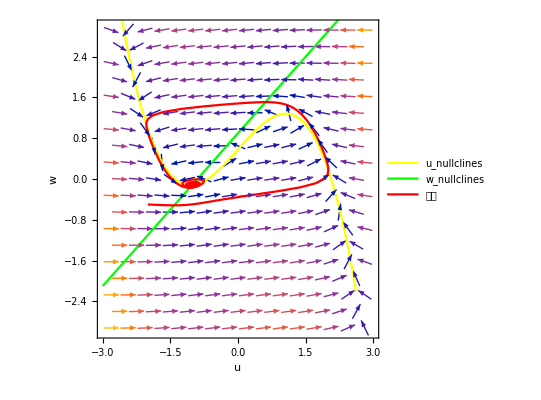

C:\Users\Administrator\Desktop\西电学习资料\Neuronal Dynamics阅读笔记\Chapter1\降维到二维\Is=58FN相图.pdf

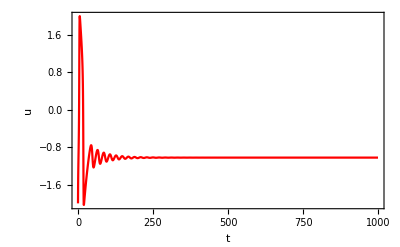

C:\Users\Administrator\Desktop\西电学习资料\Neuronal Dynamics阅读笔记\Chapter1\降维到二维\Is=58FN电压.pdf

{-0.0197841+0.305885 ⅈ,-0.0197841-0.305885 ⅈ}

```mathematica
Is=0.58;
ϵ=0.1;
b0=0.9;
b1=1; 
λ=0.3;
du=u-λ*u^3-w+Is;
dw=ϵ*(b0+b1*u-w);
linew=b0+b1*u;
lineu=u-λ*u^3+Is;
vp=VectorPlot[{du,dw},{u,-3, 3}, {w, -3, 3}];
up=Plot[lineu,{u,-3,3},PlotStyle->{Yellow},PlotLegends->{"u_nullclines"}];
wp=Plot[linew,{u,-3,3},PlotStyle->{Green},PlotLegends->{w_nullclines}];
sol=NDSolve[{u'[t]==u[t]-λ*u[t]^3-w[t]+Is,w'[t]==ϵ*(b0+b1*u[t]-w[t]),u[0]==-2,w[0]==-0.5},{u,w},{t,0,1000}];
pp=ParametricPlot[{u[t],w[t]}/.First@sol//Evaluate,{t,0,1000},PlotRange->All,PerformanceGoal->"Quality",PlotStyle->{Red},PlotLegends->{"轨迹"}];
ans=Show[{vp,up,wp,pp},Frame->True,FrameLabel->{"u","w"},LabelStyle->{FontFamily->"Times New Roman"}]
Export["C:\\Users\\Administrator\\Desktop\\西电学习资料\\Neuronal Dynamics阅读笔记\\Chapter1\\降维到二维\\Is=58FN相图.pdf",ans]
sol=NDSolve[{u'[t]==u[t]-λ*u[t]^3-w[t]+Is,w'[t]==ϵ*(b0+b1*u[t]-w[t]),u[0]==-2,w[0]==-0.5},u,{t,0,1000}];
ans=Plot[u[t]/.sol,{t,0,1000},PlotRange->All,PlotStyle->{Red},LabelStyle->{FontFamily->"Times New Roman"},Frame->True,FrameLabel->{"t","u"}]
Export["C:\\Users\\Administrator\\Desktop\\西电学习资料\\Neuronal Dynamics阅读笔记\\Chapter1\\降维到二维\\Is=58FN电压.pdf",ans]
root=NSolve[{w-lineu==0.,w-linew==0.,-3<u<3,-3<w<3},{u,w}];
F=du/.{u->v+root⟦All,1,2⟧,w->n+root⟦All,2,2⟧};
G=dw/.{u->v+root⟦All,1,2⟧,w->n+root⟦All,2,2⟧};
dFv=D[F,v]/.{v->0.000000001,n->0.000000001};
dFn=D[F,n]/.{v->0.000000001,n->0.000000001};
dGv=D[G,v]/.{v->0.000000001,n->0.000000001};
dGn=D[G,n]/.{v->0.000000001,n->0.000000001};
Eigenvalues[{{dFv⟦1⟧, dFn⟦1⟧},{dGv⟦1⟧, dGn⟦1⟧}}]
```

```mathematica
du=u-λ*u^3-w+Ism;
dw=ϵ*(b0+b1*u-w);
linew=b0+b1*u;
lineu=u-λ*u^3+Ism;
```

```mathematica
root=Table[NSolve[{w-lineu==0.,w-linew==0.,-3<u<3,-3<w<3}/.Ism->i,{u,w}],{i,0,1,0.01}];
F=du/.{u->v+root⟦All,1,1,2⟧,w->n+root⟦All,1,2,2⟧};
G=dw/.{u->v+root⟦All,1,1,2⟧,w->n+root⟦All,1,2,2⟧};
```

```mathematica
dFv=D[F,v]/.{v->0.0000000000001,n->0.0000000000001};
dFn=D[F,n]/.{v->0.0000000000001,n->0.0000000000001};
dGv=D[G,v]/.{v->0.0000000000001,n->0.0000000000001};
dGn=D[G,n]/.{v->0.0000000000001,n->0.0000000000001};
```

```mathematica
Eigenvalues1=Table[{Eigenvalues[{{dFv⟦i⟧, dFn⟦i⟧},{dGv⟦i⟧, dGn⟦i⟧}}/.Ism->i*0.01],i*0.01},{i,0,100}]
```

{{{2 List,0},0.},{{-0.707454,-0.264622},0.01},{{-0.688161,-0.270022},0.02},{{-0.668262,-0.275975},0.03},{{-0.647636,-0.282603},0.04},{{-0.626115,-0.290073},0.05},{{-0.603452,-0.298628},0.06},{{-0.579267,-0.308652},0.07},{{-0.552903,-0.320798},0.08},{{-0.523043,-0.336383},0.09},{{-0.486075,-0.359017},0.1},{{-0.41535+0.0235487 ⅈ,-0.41535-0.0235487 ⅈ},0.11},{{-0.408123+0.0711335 ⅈ,-0.408123-0.0711335 ⅈ},0.12},{{-0.400866+0.097362 ⅈ,-0.400866-0.097362 ⅈ},0.13},{{-0.393578+0.117523 ⅈ,-0.393578-0.117523 ⅈ},0.14},{{-0.386259+0.134372 ⅈ,-0.386259-0.134372 ⅈ},0.15},{{-0.378907+0.149033 ⅈ,-0.378907-0.149033 ⅈ},0.16},{{-0.371523+0.162097 ⅈ,-0.371523-0.162097 ⅈ},0.17},{{-0.364105+0.173922 ⅈ,-0.364105-0.173922 ⅈ},0.18},{{-0.356653+0.184741 ⅈ,-0.356653-0.184741 ⅈ},0.19},{{-0.349166+0.194721 ⅈ,-0.349166-0.194721 ⅈ},0.2},{{-0.341645+0.20398 ⅈ,-0.341645-0.20398 ⅈ},0.21},{{-0.334087+0.21261 ⅈ,-0.334087-0.21261 ⅈ},0.22},{{-0.326493+0.220683 ⅈ,-0.326493-0.220683 ⅈ},0.23},{{-0.318862+0.228253 ⅈ,-0.318862-0.228253 ⅈ},0.24},{{-0.311192+0.235368 ⅈ,-0.311192-0.235368 ⅈ},0.25},{{-0.303484+0.242063 ⅈ,-0.303484-0.242063 ⅈ},0.26},{{-0.295736+0.24837 ⅈ,-0.295736-0.24837 ⅈ},0.27},{{-0.287947+0.254314 ⅈ,-0.287947-0.254314 ⅈ},0.28},{{-0.280118+0.259919 ⅈ,-0.280118-0.259919 ⅈ},0.29},{{-0.272246+0.265201 ⅈ,-0.272246-0.265201 ⅈ},0.3},{{-0.26433+0.270177 ⅈ,-0.26433-0.270177 ⅈ},0.31},{{-0.256371+0.27486 ⅈ,-0.256371-0.27486 ⅈ},0.32},{{-0.248367+0.279262 ⅈ,-0.248367-0.279262 ⅈ},0.33},{{-0.240316+0.283392 ⅈ,-0.240316-0.283392 ⅈ},0.34},{{-0.232219+0.28726 ⅈ,-0.232219-0.28726 ⅈ},0.35},{{-0.224073+0.290871 ⅈ,-0.224073-0.290871 ⅈ},0.36},{{-0.215877+0.294232 ⅈ,-0.215877-0.294232 ⅈ},0.37},{{-0.207631+0.297348 ⅈ,-0.207631-0.297348 ⅈ},0.38},{{-0.199333+0.300222 ⅈ,-0.199333-0.300222 ⅈ},0.39},{{-0.190981+0.302857 ⅈ,-0.190981-0.302857 ⅈ},0.4},{{-0.182574+0.305256 ⅈ,-0.182574-0.305256 ⅈ},0.41},{{-0.174112+0.307421 ⅈ,-0.174112-0.307421 ⅈ},0.42},{{-0.165591+0.309351 ⅈ,-0.165591-0.309351 ⅈ},0.43},{{-0.157011+0.311046 ⅈ,-0.157011-0.311046 ⅈ},0.44},{{-0.148371+0.312506 ⅈ,-0.148371-0.312506 ⅈ},0.45},{{-0.139667+0.31373 ⅈ,-0.139667-0.31373 ⅈ},0.46},{{-0.130898+0.314715 ⅈ,-0.130898-0.314715 ⅈ},0.47},{{-0.122063+0.315457 ⅈ,-0.122063-0.315457 ⅈ},0.48},{{-0.113159+0.315954 ⅈ,-0.113159-0.315954 ⅈ},0.49},{{-0.104184+0.3162 ⅈ,-0.104184-0.3162 ⅈ},0.5},{{-0.0951362+0.31619 ⅈ,-0.0951362-0.31619 ⅈ},0.51},{{-0.0860123+0.315918 ⅈ,-0.0860123-0.315918 ⅈ},0.52},{{-0.0768101+0.315376 ⅈ,-0.0768101-0.315376 ⅈ},0.53},{{-0.0675268+0.314556 ⅈ,-0.0675268-0.314556 ⅈ},0.54},{{-0.0581595+0.313448 ⅈ,-0.0581595-0.313448 ⅈ},0.55},{{-0.048705+0.31204 ⅈ,-0.048705-0.31204 ⅈ},0.56},{{-0.03916+0.31032 ⅈ,-0.03916-0.31032 ⅈ},0.57},{{-0.029521+0.308274 ⅈ,-0.029521-0.308274 ⅈ},0.58},{{-0.0197841+0.305885 ⅈ,-0.0197841-0.305885 ⅈ},0.59},{{-0.00994525+0.303134 ⅈ,-0.00994525-0.303134 ⅈ},0.6},{{8.96982×10^-14+0.3 ⅈ,8.96982×10^-14-0.3 ⅈ},0.61},{{0.0100564+0.296458 ⅈ,0.0100564-0.296458 ⅈ},0.62},{{0.0202291+0.292481 ⅈ,0.0202291-0.292481 ⅈ},0.63},{{0.0305236+0.288034 ⅈ,0.0305236-0.288034 ⅈ},0.64},{{0.0409461+0.28308 ⅈ,0.0409461-0.28308 ⅈ},0.65},{{0.051503+0.277573 ⅈ,0.051503-0.277573 ⅈ},0.66},{{0.0622018+0.27146 ⅈ,0.0622018-0.27146 ⅈ},0.67},{{0.0730502+0.264676 ⅈ,0.0730502-0.264676 ⅈ},0.68},{{0.084057+0.257144 ⅈ,0.084057-0.257144 ⅈ},0.69},{{0.0952319+0.248766 ⅈ,0.0952319-0.248766 ⅈ},0.7},{{0.106586+0.239421 ⅈ,0.106586-0.239421 ⅈ},0.71},{{0.11813+0.228952 ⅈ,0.11813-0.228952 ⅈ},0.72},{{0.12988+0.217153 ⅈ,0.12988-0.217153 ⅈ},0.73},{{0.141848+0.203738 ⅈ,0.141848-0.203738 ⅈ},0.74},{{0.154055+0.188298 ⅈ,0.154055-0.188298 ⅈ},0.75},{{0.166518+0.170201 ⅈ,0.166518-0.170201 ⅈ},0.76},{{0.179261+0.148368 ⅈ,0.179261-0.148368 ⅈ},0.77},{{0.192312+0.120638 ⅈ,0.192312-0.120638 ⅈ},0.78},{{0.205702+0.0809076 ⅈ,0.205702-0.0809076 ⅈ},0.79},{{0.264872,0.174069},0.8},{{0.340108,0.127217},0.81},{{0.394414,0.10226},0.82},{{0.442955,0.0841774},0.83},{{0.489156,0.0697342},0.84},{{0.534633,0.0575714},0.85},{{0.580476,0.046956},0.86},{{0.627686,0.0374219},0.87},{{0.67748,0.0286206},0.88},{{0.731807,0.0202202},0.89},{{0.795058,0.0117245},0.9},{{0.9,0.},0.91},{{0.795058,0.0117245},0.92},{{0.731807,0.0202202},0.93},{{0.67748,0.0286206},0.94},{{0.627686,0.0374219},0.95},{{0.580476,0.046956},0.96},{{0.534633,0.0575714},0.97},{{0.489156,0.0697342},0.98},{{0.442955,0.0841774},0.99},{{0.394414,0.10226},1.}}